```mathematica
ClearAll["Global`*"]
```

```mathematica
(*test case 1*)
```

```mathematica
(*u[x_]:=Cos[2 π x/L]
gradu[x_]:=(-2 π  Sin[(2 π x)/L])/L*)
```

```mathematica
(*test case 2*)
```

```mathematica
u[x_]:=Cos[2 π x^2/L]
```

```mathematica
gradu[x_]:=-(4 π x Sin[(2 π x^2)/L])/L
```

```mathematica
L=1;
```

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/u.csv"][[2;;]];
(*the solution obtained from finite elements is not unique -> it is determined up to a constant-> substract it off so you can compare with the exact one*)
t0=t[[1,1]];
t=Table[{t[[i,2]],t[[i,1]]- t0+u[0]},{i,2,Length[t]}]
```

{{0.9,0.368127},{0.8,-0.637421},{0.7,-0.998025},{0.6,-0.637423},{0.5,8.82016×10^-7},{0.4,0.535828},{0.3,0.844328},{0.2,0.968583},{0.1,0.998027},{0.,1.}}

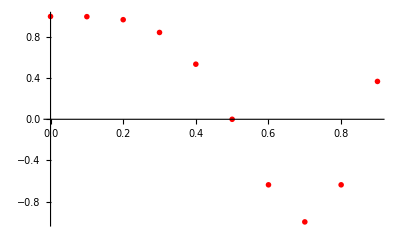

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

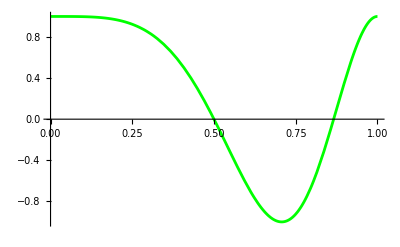

```mathematica
plotexact=Plot[u[x],{x,0,L},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

2.82663×10^-6

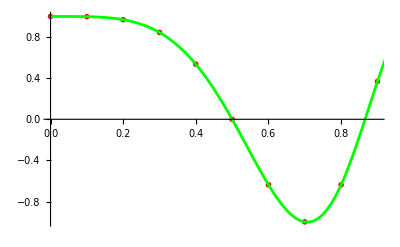

```mathematica
Show[plotnum,plotexact]
```

```mathematica
(*check for grad u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/grad_u.csv"][[2;;]];
(*the solution obtained from finite elements is not unique -> it is determined up to a constant-> substract it off so you can compare with the exact one*)
t0=t[[1,1]];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.9,10.5056},{0.8,7.74513},{0.7,-0.548779},{0.6,-5.80722},{0.5,-6.28303},{0.4,-4.24475},{0.3,-2.0206},{0.2,-0.625357},{0.1,-0.0797785},{0.,-0.00804412}}

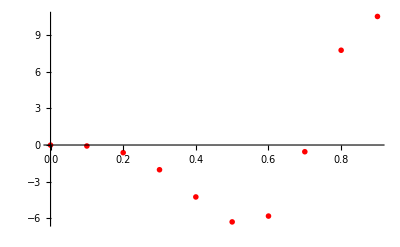

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

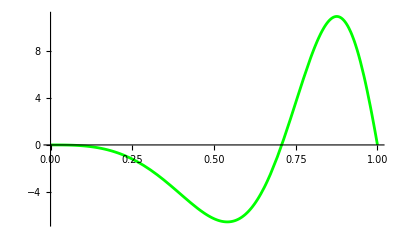

```mathematica
plotexact=Plot[gradu[x],{x,0,L},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-gradu[t[[i,1]]]],{i,1,Length[t]}]]
```

0.00992999

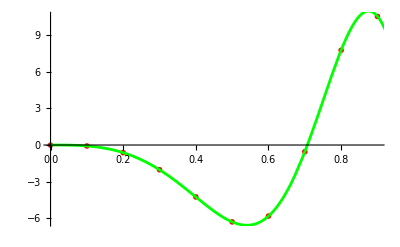

```mathematica
Show[plotnum,plotexact]
```